Copyright ©, 2015, Erdong Guo and Shu Lin
Author: Erdong Guo and Shu Lin
E-mail: guoerdong@itp.ac.cn, linshu8@mail.sysu.edu.cn
Affliation: Institute of Theoretical Physics, Chinese Academy of Scineces, School of Physics and Astronomy, Sun-Yat Sen University
Description: Calculation tools for AdS/QCD. In this file, we calcualte the mass term in the anomaly relation which corrsponds to the \frac{\partial{S}}{\partial{\phi}}, here S represents the on-shell action in the bulk. The hydro effects of the mass term also investigated by numerical calculation.

```mathematica
Quit[]
```

```mathematica
H=1+1/#^4&;f=1-1/#^4&;
gtt=-r0^2/2 #^2 f[#]^2/H[#]&;
gxx=r0^2/2 #^2 H[#]&;
gphiphi=chi[#]^2&;
grhorho=1/#^2&;
sq=Function[rho,Simplify[Sqrt[-gtt[rho]gxx[rho](gxx[rho]^2+B^2)(1+rho^2chi'[rho]^2/(1-chi[rho]^2))grhorho[rho](1-chi[rho]^2)^3],Assumptions->rho>1&&r>0&&r0>0]];
L=Simplify[Sqrt[-gtt[rho] gxx[rho](gxx[rho]^2+B^2)(grhorho[rho]+chi'[rho]^2/(1-chi[rho]^2))(1-chi[rho]^2)^3]/.{r0-> 1},Assumptions->rho>1&&chi[rho]<1&&chi[rho]>0];
eom=3 (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi[rho]^3-(-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi[rho] (3+4 rho^2 chi'[rho]^2)+rho (-(3+rho^4 (3+4 B^2 (1+3 rho^4)+5 (rho^4+rho^8))) chi'[rho]-4 rho^2 (1+rho^4) (1+2 B^2 rho^4+rho^8) chi'[rho]^3-rho (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi''[rho])+rho chi[rho]^2 ((3+rho^4 (3+4 B^2 (1+3 rho^4)+5 (rho^4+rho^8))) chi'[rho]+rho (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi''[rho]);
eom1=Simplify[ome^2sq[rho]gphiphi[rho]/gtt[rho]phi[rho]-D[sq[rho]gphiphi[rho]/grhorho[rho]phi'[rho],rho]+D[(1-chi[rho]^2)^2,rho]B Az[rho](I ome)];
eom2=Simplify[ome^2sq[rho]/(gtt[rho]gxx[rho])Az[rho]-D[sq[rho]/(grhorho[rho]gxx[rho])Az'[rho],rho]-D[(1-chi[rho]^2)^2,rho]B phi[rho](I ome)];
rtab={{a1->(I a0 ome)/(4 r0),a2->(ome (48 I B b0 r0 √(-(B^2+r0^4) (-1+chi0^2)^3)-I a0 (-1+chi0^2) (r0^4 (6 r0^2 (2+7 chi0^2)-8 I r0 (-1+chi0^2) ome-(-1+chi0^2) ome^2)+B^2 (r0^2 (-20+74 chi0^2)-8 I r0 (-1+chi0^2) ome-(-1+chi0^2) ome^2))))/(32 r0^2 (B^2+r0^4) (-1+chi0^2)^2 (2 r0-I ome)),a3->-(ome (4 I r0+ome) (144 B b0 r0 √(-(B^2+r0^4) (-1+chi0^2)^3)-a0 (-1+chi0^2) (r0^4 (2 r0^2 (22+59 chi0^2)-16 I r0 (-1+chi0^2) ome-(-1+chi0^2) ome^2)+B^2 (r0^2 (-52+214 chi0^2)-16 I r0 (-1+chi0^2) ome-(-1+chi0^2) ome^2))))/(384 r0^3 (B^2+r0^4) (-1+chi0^2)^2 (2 r0-I ome)),b1->(I b0 ome)/(4 r0),b2->-(I ome (48 a0 B r0^3 chi0^2 √(-(B^2+r0^4) (-1+chi0^2)^3)+b0 r0^4 (-1+chi0^2) (r0^2 (4+50 chi0^2)-8 I r0 (-1+chi0^2) ome-(-1+chi0^2) ome^2)+B^2 b0 (-1+chi0^2) (r0^2 (-28+82 chi0^2)-8 I r0 (-1+chi0^2) ome-(-1+chi0^2) ome^2)))/(32 r0^2 (B^2+r0^4) (-1+chi0^2)^2 (2 r0-I ome)),b3->(I (4 r0-I ome) ome (144 a0 B r0^3 chi0^2 √(-(B^2+r0^4) (-1+chi0^2)^3)+b0 r0^4 (-1+chi0^2) (2 r0^2 (10+71 chi0^2)-16 I r0 (-1+chi0^2) ome-(-1+chi0^2) ome^2)+B^2 b0 (-1+chi0^2) (r0^2 (-76+238 chi0^2)-16 I r0 (-1+chi0^2) ome-(-1+chi0^2) ome^2)))/(384 r0^3 (B^2+r0^4) (-1+chi0^2)^2 (2 r0-I ome))}};
chih=chi0-3/4 (-1+rho)^2 chi0+3/4 (-1+rho)^3 chi0;
pchih=-3/2 (-1+rho) chi0+9/4 (-1+rho)^2 chi0;
phih=(rho-1)^(-I ome/(2 r0))(a0+a1(rho-1)+a2(rho-1)^2+a3(rho-1)^3)/.rtab;
pphih=D[phih,rho];
Ah=(rho-1)^(-I ome/(2 r0))(b0+b1(rho-1)+b2(rho-1)^2+b3(rho-1)^3)/.rtab;
pAh=D[Ah,rho];
Indr[Chi0_,omg_,nB_,eps_,uv_]:=Module[{sola0,solb0,m,lam,A0,f1,Oeta,CEB},
sola0=NDSolve[{eom==0,eom1==0,eom2==0,chi[1+eps]==chih/.{rho->1+eps},chi'[1+eps]==pchih/.{rho->1+eps},phi[1+eps]==phih/.{rho->1+eps},phi'[1+eps]==pphih/.{rho->1+eps},Az[1+eps]==Ah/.{rho->1+eps},Az'[1+eps]==pAh/.{rho->1+eps}}/.{chi0->Chi0,ome->omg,B->nB,r0->1,a0->1,b0->0},{chi,phi,Az},{rho,1+eps,uv},WorkingPrecision->15][[-1]];
solb0=NDSolve[{eom==0,eom1==0,eom2==0,chi[1+eps]==chih/.{rho->1+eps},chi'[1+eps]==pchih/.{rho->1+eps},phi[1+eps]==phih/.{rho->1+eps},phi'[1+eps]==pphih/.{rho->1+eps},Az[1+eps]==Ah/.{rho->1+eps},Az'[1+eps]==pAh/.{rho->1+eps}}/.{chi0->Chi0,ome->omg,B->nB,r0->1,a0->0,b0->1},{chi,phi,Az},{rho,1+eps,uv},WorkingPrecision->15][[-1]];m=(rho chi[rho]/.{rho->uv})/.sola0;lam=-(phi[uv]/.sola0)/(phi[uv]/.solb0);A0=(Az[uv]/.sola0)+lam(Az[uv]/.solb0);f1=uv^3((phi'[uv]/.sola0)+lam(phi'[uv]/.solb0))/(-2);Oeta=2(r0^2/2)^2m^2f1/.{r0->1};CEB=nB A0(I omg);{Oeta,CEB,Abs[Oeta/CEB],-N[1-(1-Chi0^2)^2]}]
```

Black hole imdedding when mass is 2/5, 1/2, 3/5 and B is 1

```mathematica
chii[1,2/5]=Rationalize[{0.2661,0.4}];
chii[1,1/2]=Rationalize[{0.3347,0.5}];
chii[1,3/5]=Rationalize[{0.4048,0.6}];
chii[1,7/20]=Rationalize[{0.2322,7/20}];
```

```mathematica
dataomee[init_,stepl_,m_,nn_,nB_]:=
Module[{data,function,i},data=Table[{init+i stepl,Indr[chii[nB,m][[1]],init+i stepl,nB,1/100,100][[-2]][[-1]]},{i,nn}];
function=ListInterpolation[Table[{Indr[chii[nB,m][[1]],init+i stepl,nB,1/100,100][[-2]][[-1]],init+i stepl},{i,nn}],{{init+stepl,init+nn stepl}}];
Show[ListPlot[data,AxesLabel->{Style["ω",FontSize-> 18],Style["O_η/CEB",FontSize->18]},AxesOrigin->{0,0},PlotStyle->Blue],ListLinePlot[data,AxesLabel->{Style["ω",FontSize-> 18],Style["O_η/CEB",FontSize->18]},AxesOrigin->{0,0},PlotStyle-> Hue[m-7/20],InterpolationOrder->5](*Plot[function[x],{x,init+stepl,nn stepl},AxesLabel->{Style["B",FontSize-> 18],Style["O_η/CEB",FontSize->18]},PlotStyle-> Hue[m-7/20],AxesOrigin->{0,0}],PlotRange->All]*)]]
```

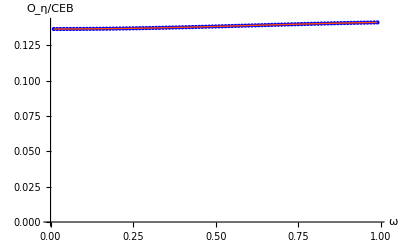

```mathematica
dataomee[0,1/100,2/5,99,1]
```

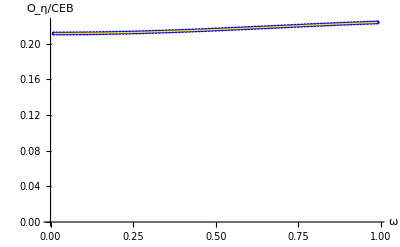

```mathematica
dataomee[0,1/100,1/2,99,1]
```

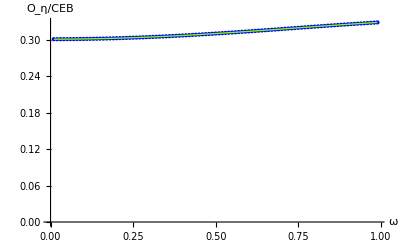

```mathematica
dataomee[0,1/100,3/5,99,1]
```

```mathematica
dataomee[0,1/100,7/20,99,1]
```

```mathematica
Indrp[Chi0_,omg_,nB_,eps_,uv_]:=Module[{sola0,solb0,m,lam,A0,f1,Oeta,CEB},
sola0=NDSolve[{eom==0,eom1==0,eom2==0,chi[1+eps]==chih/.{rho->1+eps},chi'[1+eps]==pchih/.{rho->1+eps},phi[1+eps]==phih/.{rho->1+eps},phi'[1+eps]==pphih/.{rho->1+eps},Az[1+eps]==Ah/.{rho->1+eps},Az'[1+eps]==pAh/.{rho->1+eps}}/.{chi0->Chi0,ome->omg,B->nB,r0->1,a0->1,b0->0},{chi,phi,Az},{rho,1+eps,uv},WorkingPrecision->15][[-1]];
solb0=NDSolve[{eom==0,eom1==0,eom2==0,chi[1+eps]==chih/.{rho->1+eps},chi'[1+eps]==pchih/.{rho->1+eps},phi[1+eps]==phih/.{rho->1+eps},phi'[1+eps]==pphih/.{rho->1+eps},Az[1+eps]==Ah/.{rho->1+eps},Az'[1+eps]==pAh/.{rho->1+eps}}/.{chi0->Chi0,ome->omg,B->nB,r0->1,a0->0,b0->1},{chi,phi,Az},{rho,1+eps,uv},WorkingPrecision->15][[-1]];m=(rho chi[rho]/.{rho->uv})/.sola0;lam=-(phi[uv]/.sola0)/(phi[uv]/.solb0);A0=(Az[uv]/.sola0)+lam(Az[uv]/.solb0);f1=uv^3((phi'[uv]/.sola0)+lam(phi'[uv]/.solb0))/(-2);Oeta=2(r0^2/2)^2m^2f1/.{r0->1};CEB=nB A0(I omg);{Oeta,CEB,-Im[Log[Oeta/(CEB Abs[Oeta/CEB])]]}]
```

```mathematica
Indrp[1/5,1/100,1,1/100,100]
```

{{0.1550815637077+0.0000241380091166 ⅈ},{-1.9802486161525+0.014018212115242 ⅈ},{3.134358108409}}

```mathematica
Indrp[4/5,2/100,1,1/100,100][[-1]][[-1]]
```

3.137136011109

```mathematica
dataomee[init_,stepl_,m_,nn_,nB_]:=
Module[{data,function,i},data=Table[{init+i stepl,(Indrp[chii[nB,m][[1]],init+i stepl,nB,1/100,100][[-1]][[-1]])/(init+i stepl) },{i,nn}];
function=ListInterpolation[Table[{(Indrp[chii[nB,m][[1]],init+i stepl,nB,1/100,100][[-2]][[-1]])/ (init+i stepl)},{i,nn}],{{init+stepl,init+nn stepl}}];
Show[ListPlot[data,AxesLabel->{Style["ω",FontSize-> 18],Style["δt",FontSize->18]},AxesOrigin->{0,0},PlotStyle->Blue],ListLinePlot[data,AxesLabel->{Style["ω",FontSize-> 18],Style["δt",FontSize->18]},AxesOrigin->{0,0},PlotStyle-> Hue[m-7/20],InterpolationOrder->5](*Plot[function[x],{x,init+stepl,nn stepl},AxesLabel->{Style["B",FontSize-> 18],Style["O_η/CEB",FontSize->18]},PlotStyle-> Hue[m-7/20],AxesOrigin->{0,0}],PlotRange->All]*)]]
```

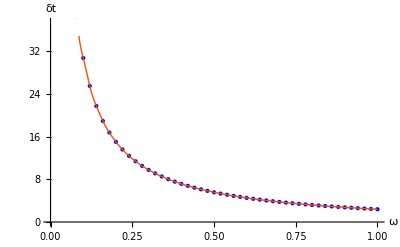

```mathematica
dataomee[0,1/50,2/5,50,1]
```

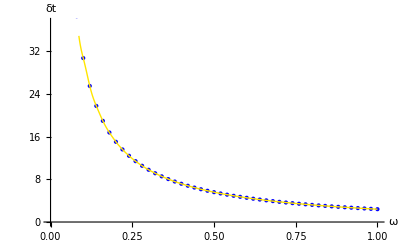

```mathematica
dataomee[0,1/50,1/2,50,1]
```

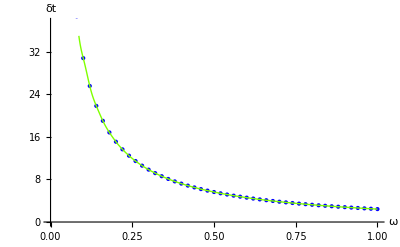

```mathematica
dataomee[0,1/50,3/5,50,1]
```

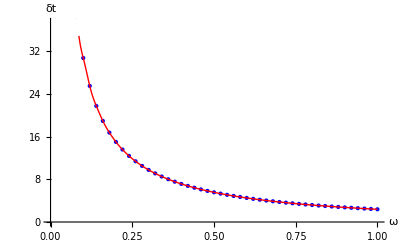

```mathematica
dataomee[0,1/50,7/20,50,1]
```

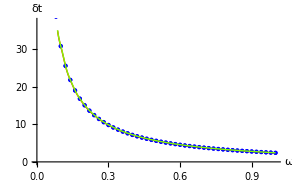

```mathematica
Show[%,%61]
```